{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→Medium,FrameStyle→Directive[GrayLevel[0]],{PlotLegends→Placed[{cos((2  π)/2t),sin((2  π)/2t)},Top]}}

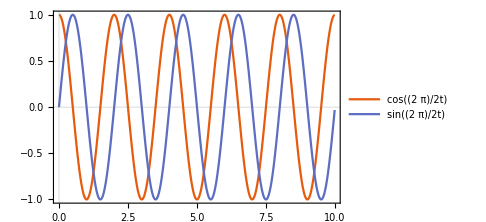

```mathematica
ClearAll["Global`*"];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]];
AppendTo[plot2Doption,{PlotLegends->Placed[{"cos((2  π)/2t)","sin((2  π)/2t)"},Top]}]

result=Transpose@Import[FileNameJoin[{NotebookDirectory[],"example1_dataOrg.dat"}]];
time=result[[1]];
ListPlot[Table[Transpose@{time,result[[i]]},{i,2,Length@result}],
Joined->True,
Evaluate[plot2Doption]]
```

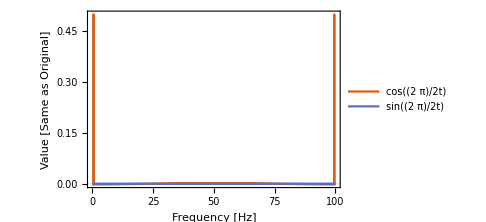
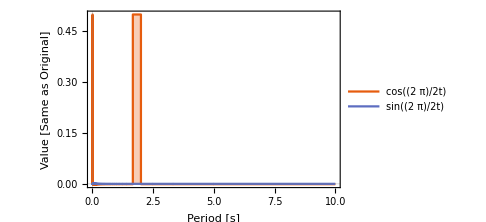

```mathematica
dataRe=Transpose@Import[FileNameJoin[{NotebookDirectory[],"example1_dataDFT_Re.dat"}]];
freq=dataRe[[1]];

Row[{ListStepPlot[Table[Transpose[{freq[[2;;]],dataRe[[i]][[2;;]]}],{i,2,Length@dataRe}],
Filling->Axis,
FrameLabel->{"Frequency [Hz]","Value [Same as Original]"},
PlotRange->{All,All},
Evaluate[plot2Doption]]
,
ListStepPlot[Table[Transpose[{1/freq[[2;;]],dataRe[[i]][[2;;]]}],{i,2,Length@dataRe}],
Filling->Axis,
FrameLabel->{"Period [s]","Value [Same as Original]"},
PlotRange->{All,All},
Evaluate[plot2Doption]
]}]
```

```mathematica
""
```

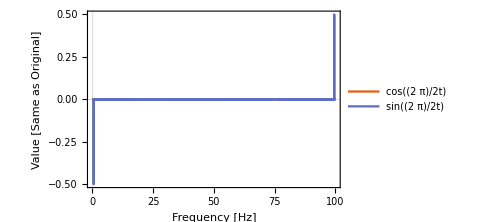
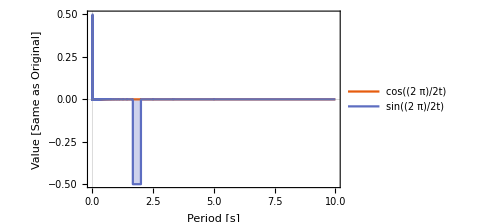

```mathematica
dataIm=Transpose@Import[FileNameJoin[{NotebookDirectory[],"example1_dataDFT_Im.dat"}]];
freq=dataIm[[1]];

Row[{ListStepPlot[Table[Transpose[{freq[[2;;]],dataIm[[i]][[2;;]]}],{i,2,Length@dataIm}],
Filling->Axis,
FrameLabel->{"Frequency [Hz]","Value [Same as Original]"},
PlotRange->{All,All},
Evaluate[plot2Doption]]
,
ListStepPlot[Table[Transpose[{1/freq[[2;;]],dataIm[[i]][[2;;]]}],{i,2,Length@dataIm}],
Filling->Axis,
FrameLabel->{"Period [s]","Value [Same as Original]"},
PlotRange->{All,All},
Evaluate[plot2Doption]
]}]
```